```mathematica
Clear[interPP,isumPP ,isumZP,isumZZ,isumWW,isumWWdyt]
SetDirectory[NotebookDirectory[]];
interPP = Get["intang_PPtt_3TeV_fix.txt"];
interZP = Get["intang_ZPtt_3TeV_fix.txt"];
```

```mathematica
interWW = Get["intang_WWtt1_3TeV.txt"];
interZZ = Get["intang_ZZtt_3TeV_Fix.txt"];
```

```mathematica
dytinterWW = Get["intang_WWttDYT_3TeV_20_new.txt"];
dytinterWW11= Get["intang_WWttDYT11_3TeV_20_new.txt"];
dytinterWWm1m1= Get["intang_WWttDYTm1m1_3TeV_20.txt"];
dytinterZZ = Get["intang_ZZtt00DYT_3TeV_20_new.txt"];
dytinterZZ11= Get["intang_ZZtt11DYT_3TeV_20.txt"];
dytinterZZm1m1= Get["intang_ZZttm1m1DYT_3TeV_20.txt"];
dytt = Table[(1/1000)*(20i-200),{i,0,20}]
```

{-1/5,-9/50,-4/25,-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25,7/50,4/25,9/50,1/5}



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
dytt[[11]]
```

0

```mathematica
angenPP[ang_,num_] :=interPP[[ang]] [(1 + ((num - 350)/50))]

angenZP[ang_,num_] :=interZP[[ang]] [(1 + ((num - 350)/50))]

angenWW[ang_,num_] :=interWW[[ang]][(1 + ((num - 350)/50))]

angenZZ[ang_,num_] :=interZZ[[ang]][(1 + ((num - 350)/50))]
```

```mathematica
isumWWdyt[ang_,dyt_,energy_] :=dytinterWW[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdyt11[ang_,dyt_,energy_] :=dytinterWW11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytm1m1[ang_,dyt_,energy_] :=dytinterWWm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt00[ang_,dyt_,energy_] :=dytinterZZ[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt11[ang_,dyt_,energy_] :=dytinterZZ11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdytm1m1[ang_,dyt_,energy_] :=dytinterZZm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
lum = 1;
br = 0.2963;
sqrtsbin = Table[350+50*i,{i,0,54}];
```

```mathematica
background = Table[NIntegrate[br*lum*(angenPP[k,ss]+angenWW[k,ss]+angenZP[k,ss]+angenZZ[k,ss]),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18}];
```

```mathematica
signal = Table[NIntegrate[br*lum*(isumWWdyt[k,j,ss]+isumWWdyt11[k,j,ss]+isumWWdytm1m1[k,j,ss]+isumZZdyt00[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18},{j,1,Length@dytt}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
(*Sum angles*)
sumanglesbkg = Table[Sum[background[[i,n]],{n,1,18}],{i,1,53}];
sumanglessig = Table[Sum[signal[[i,n,j]],{n,1,18}],{i,1,53},{j,1,Length@dytt}];
```

```mathematica
sqrtsumanglesbkg =Sqrt[sumanglesbkg];
```

```mathematica
chi2sumang = Table[Sum[(sumanglessig [[i,j]]/sqrtsumanglesbkg [[i]])^2,{i,1,53}],{j,1,Length@dytt}];
```

```mathematica
chi = chi2sumang  ;
```

```mathematica
dytt = Table[(1/1000)*(20i-200),{i,0,20}]
dytchi2en = Table[{dytt[[k]],chi[[k]]},{k,1,Length@dytt}];
intdytchi2en = Interpolation[dytchi2en ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

{-1/5,-9/50,-4/25,-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25,7/50,4/25,9/50,1/5}

InterpolatingFunction[…]

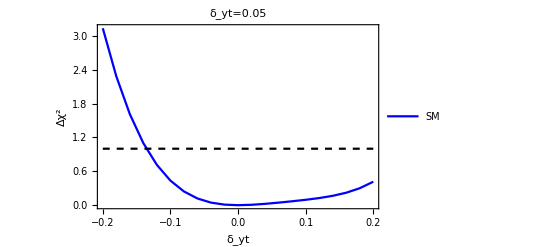

```mathematica
ListPlot[{intdytchi2en ,sig1},Joined->True,Frame->True,PlotStyle->{Blue,{Dashed,Black}},PlotLabel->Style["δ_yt=0.05",Black,20],PlotLegends->{"SM"},FrameLabel->{Style["δ_yt",Black,20],Style["Δχ^2",Black,15]},FrameTicksStyle->Directive[Black,13]]
```

```mathematica
(*bin angle and energy*)
sqrtback = Sqrt[background];
chi2 = Table[Sum[(signal[[i,j,k]]/ sqrtback[[i,j]])^2,{i,1,33},{j,1,18}],{k,1,Length@dytt}];
```

```mathematica
dytchi2enang = Table[{dytt[[k]],chi2 [[k]]},{k,1,Length@dytt}];
intdytchi2enang = Interpolation[dytchi2enang ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

InterpolatingFunction[…]

```mathematica
dyttnew = Table[(1/1000)*(i-200),{i,0,400}];
```

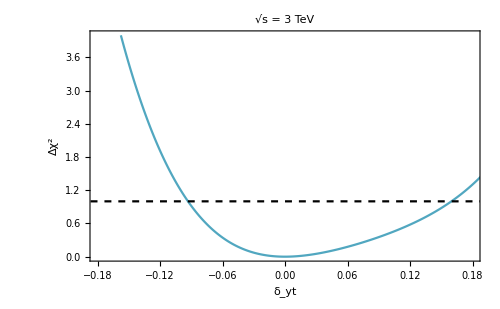

```mathematica
lineplot=ListPlot[{Transpose[{ dyttnew ,intdytchi2enang [dyttnew]}],sig1},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],{Dashed,Black}},Frame->True,FrameLabel->{Style[DisplayForm["δ_yt"],Black,20,FontFamily->"Times"],Style["Δχ^2",Black,19,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",3 TeV}]  ,Black,18,FontFamily->"Times"],
PlotRange->{{-0.18,0.18},{0,4}},
FrameTicksStyle->Directive[Black,17],ImageSize->500]
```

```mathematica
Export["chi_square_3TeV_2j2l.pdf",lineplot]
```

chi_square_3TeV_2j2l.pdf

```mathematica
Sqrt[br] * 10
```

5.44334